# Thunderstorm Analyzer

ABSTRACT:
The goal of this project is the creation of a system which will automatically get the data from public weather servers, analyze quantities like the number of cosmic rays, levels of ionizing radiation, electrostatic field strength, etc., and study their temporal correlation to detect the cases of Thunderstorm ground enhancements (TGE).
Thunderstorm ground Enhancement is a process of increase in the level of gamma radiation, number of electrons and neutrons, connected to the propagation of cosmic rays through strong atmospheric electric fields.
It was observed that during thunderstorms electrostatic field increases by orders of magnitude and gamma radiation levels as well as number of neutrons and relativistic electrons increase up to 10 times above cosmic ray background. When electrostatic field reaches certain levels lightning happens and the level of gamma radiation, electrons and neutrons as well as the field itself fall down immediately after the lightning.
The TGE events are characterized by following 7 criteria:

Large fluxes of electrons and gamma rays with durations around 10 minutes;

Increase in neutron number;

Microsecond electron bursts with around 50ms duration;

Increase of high energy muon level;

Large, usually negative, near-surface electric field, rising sometimes from deep negative to near zero positive values. Usually field is at the level of -10 - -30 kV/m;

Decrease of the cloud-ground lightnings and increase of intra-cloud lightnings.

Increase of relative humidity above 80% and decrease of air temperature below 5-6 degrease Celsius.

The system should analyze all the data and look for this kind of events and notify us upon their occurring.

## Import Weather Data from csv file.

#### Delete corrupted sublists and the first element of the list which contains header of csv file.

#### Data importer from csv file.

```mathematica
dataImporter[filePath_String, nOfColumns_Integer]:=Select[
	DeleteCases[
		Delete[
			Import[
				StringJoin[
					NotebookDirectory[], filePath
				]
			],
			1
		],
		"", {2}
	],
	(Length[#] == nOfColumns)&
];
```

#### Conversion rule for converting month names to month numbers.

```mathematica
monthRule:={"Jan"->1,"Feb"->2,"Mar"->3,"Apr"->4,"May"->5,"Jun"->6,"Jul"->7,"Aug"->8,"Sep"->9,"Oct"->10,"Nov"->11,"Dec"->12};
```

#### Transforms the date to the format of {y, m, d, h, m, s}

```mathematica
dateFormater[inputList_] := Replace[
	Part[
		MapAt[
			ToExpression,
			ReplaceAll[
				StringSplit[
					inputList,
					":" | " " | "-"
				],
				monthRule],
			{All,{1,2,3,4,5,6}}
		],All, {3, 2, 1, 4, 5, 6}
	],
	{year_, rest__} :> {year+2000, rest},
	{1}
];
```

### Import Electric Filed Data

```mathematica
electricFieldFull = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\Electric_Field_MAKET.csv", 2];

electricFieldFullConverted = Transpose[{dateFormater[electricFieldFull[[All,1]]], electricFieldFull[[All,2]]}];
```

```mathematica
electricField = Part[
	electricFieldFullConverted,
	Position[
		electricFieldFullConverted,
		{2016, 7, 6, 06, 00, 00.}][[1, 1]] ;; Position[electricFieldFullConverted, {2016, 7, 6, 14, 00, 00.}][[1, 1]]
];
```

### Import STAND Electron and Gamma ray Detector Data

```mathematica
stand1Raw = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\Stand_1cm.csv", 13];

stand1 = Transpose[{dateFormater[stand1Raw[[All,1]]],stand1Raw[[All,2]]}];
stand1Normalized = Transpose[{dateFormater[stand1Raw[[All,1]]],N[Rescale[stand1Raw[[All,2]],{Min[stand1],Max[stand1]},{0, 20}]]}];
```

### Import NaI Electron and Gamma ray Detector Data

```mathematica
naIFull = dataImporter["Weather Data (05.Jul - 07.Jul.16)\\NaI.csv",19];
naIFull = naIFull[[4;;]];

naI3 = Transpose[
	{dateFormater[naIFull[[All, 1]]], naIFull[[All, 3]]}
];
```

### Import temperature and humidity data.

```mathematica
weatherData = Select[
	Delete[
		Import[
			StringJoin[NotebookDirectory[],"Weather Data (05.Jul - 07.Jul.16)\\Weather_Station.csv"]
		],
		1
	],
	(Length[#] == 37)&
];

weatherDataOrder = {
	{1,"Date/Time"},{2,"Outside Temperature"},{3,"Hi Temperature"},{4,"Low Temperature"},{5,"Outside Humidity"},
	{6,"Dew Point"},{7,"Wind Speed"},{8,"Wind Direction"},{9,"Wind Run"},{10,"Hi Wind Speed"},{11,"Hi Wind Direction"},
	{12,"Wind Chill"},{13,"Heat Index"},{14,"THW Index"},{15,"THWS Index"},{16,"Pressure"},{17,"Rain"},
	{18,"Rain Rate"},{19,"Solar Radiation"},{20,"Solra Energy"},{21,"Hi Solar Radiation"},{22,"UV Index"},{23,"UV Dose"},
	{24,"Hi UV"},{25,"Heating D-D"},{26,"Cooling D-D"},{27,"Inside Temperature"},{28,"Inside Humidity"},{29,"Inside Dew Point"},
	{30,"Inside Heat"},{31,"Inside EMC"},{32,"Inside Air Density"},{33,"ET"},{34,"Wind Samp"},{35,"Wind TX"},{36,"ISS Recept"},{37,"Arc Int\n"}
};

temperature = Transpose[{dateFormater[weatherData[[All, 1]]], weatherData[[All, 2]]}];
humidity = Transpose[{dateFormater[weatherData[[All, 1]]], weatherData[[All, 5]]}];
```

```mathematica
ClearAll[plotOriginalEField]
```

#### Generate the plot of electric field

```mathematica
(*eFieldplottingRange = {{{2016,8,1,11,00,00},{2016,8,1,12,00,00}},{-20,20}};*)
(*eFieldplottingRange = {{{2016,8,1,11,30,00},{2016,8,1,11,45,00}},{-20,20}};*)
eFieldPlottingRange = Full;
naI3PlottingRange = Full;
```

```mathematica
plotOriginal[data_, rangeMin_, rangeMax_, rangeStep_] := DateListPlot[
	data,
	Filling->Axis,
	PlotRange->plottingRange,
	Joined->False,
	PlotTheme->"Detailed",
	FrameTicks->{{Range[rangeMin, rangeMax, rangeStep],None},All}
]
```

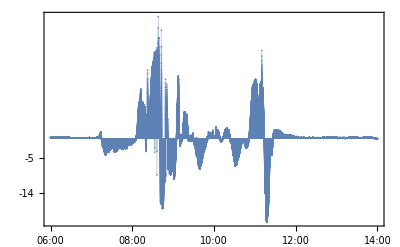

```mathematica
plotEField=plotOriginal[electricField,-50,50, 1]
```

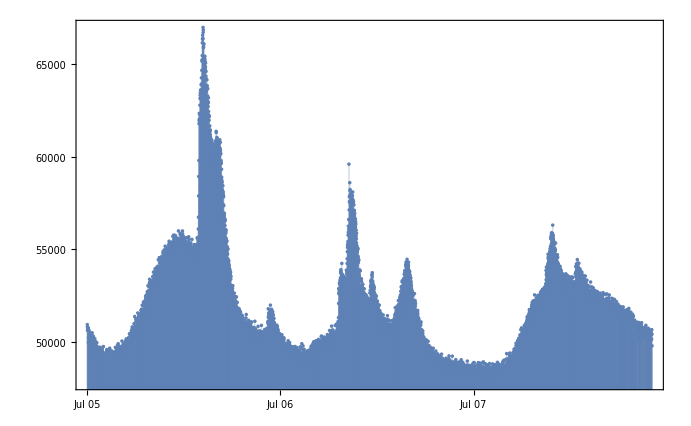

```mathematica
plotNaI3=plotOriginal[naI3,30000,70000,1000]
```

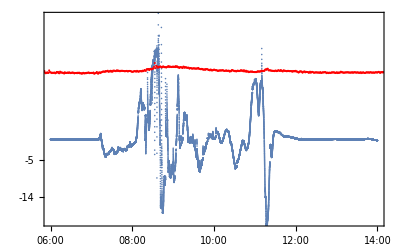

```mathematica
Show[DateListPlot[electricField,PlotRange->{-20,30},Joined->False,PlotTheme->"Detailed",
	FrameTicks->{{Range[-50,50,1],None},All}],DateListPlot[stand1Normalized,PlotRange->Full,PlotStyle->Red,Joined->False]]
```

#### Get local minima and maxima in time series and apply a low cut filters

```mathematica
getMaxs[detectorData_, sigma_, sharpness_, triggerShreshold_] := DeleteCases[
	Pick[
		detectorData,
		PeakDetect[
			detectorData[[All, 2]],
			sigma,
			sharpness
		],
		1
	],
	{date_,data_}/;data ≥ triggerShreshold
];
getMaxs[detectorData_, sigma_, sharpness_] := Pick[
	detectorData,
	PeakDetect[
		detectorData[[All, 2]],
		sigma,
		sharpness
	],
	1
];

getMins[detectorData_, sigma_, sharpness_, triggerShreshold_] := DeleteCases[
	Pick[
		detectorData,
		PeakDetect[
			-detectorData[[All, 2]],
			sigma,
			sharpness
		],
		1
	],
	{date_,data_}/;data ≥ triggerShreshold
];
getMins[detectorData_, sigma_, sharpness_] := Pick[
	detectorData,
	PeakDetect[
		-detectorData[[All, 2]],
		sigma,
		sharpness
	],
	1
];
```

```mathematica
eFieldMins=getMins[electricField, 30, 0, -7];
eFieldMaxs=getMaxs[electricField, 50, 0, -0.5];
```

```mathematica
naI3Mins = getMins[naI3, 50, 0.3];
naI3Maxs = getMaxs[naI3,15, 1.3];
```

#### Construct a graph of a data with minimas and maximas.

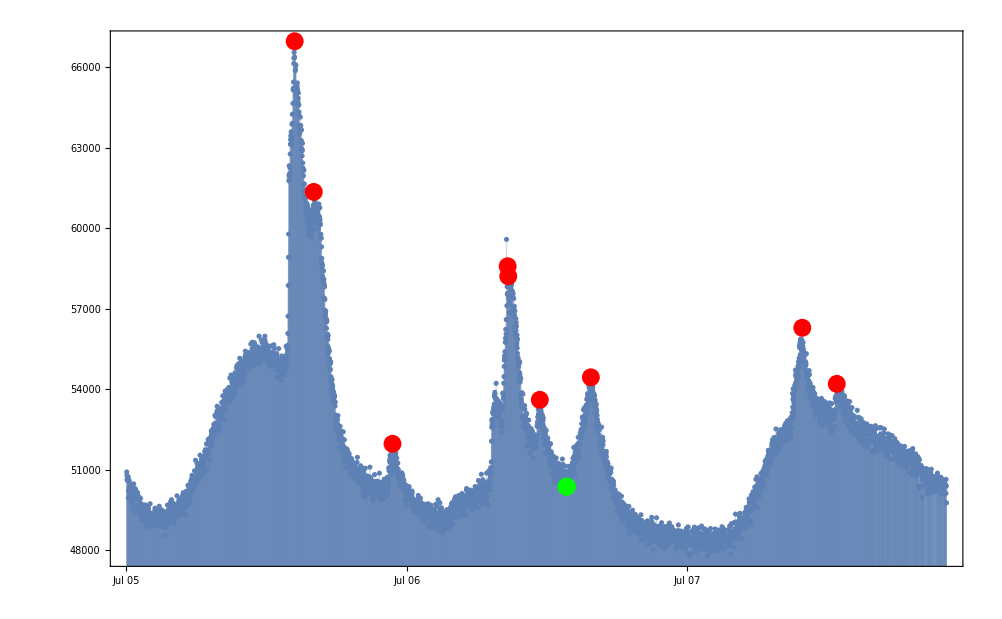

```mathematica
Show[
 	plotNaI3,
 	DateListPlot[
  		naI3Maxs,
  		PlotStyle -> Red,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	],
 	DateListPlot[
  		naI3Mins,
  		PlotStyle -> Green,
  		PlotRange -> naI3PlottingRange,
  		Joined -> False
  	]
 ]
```

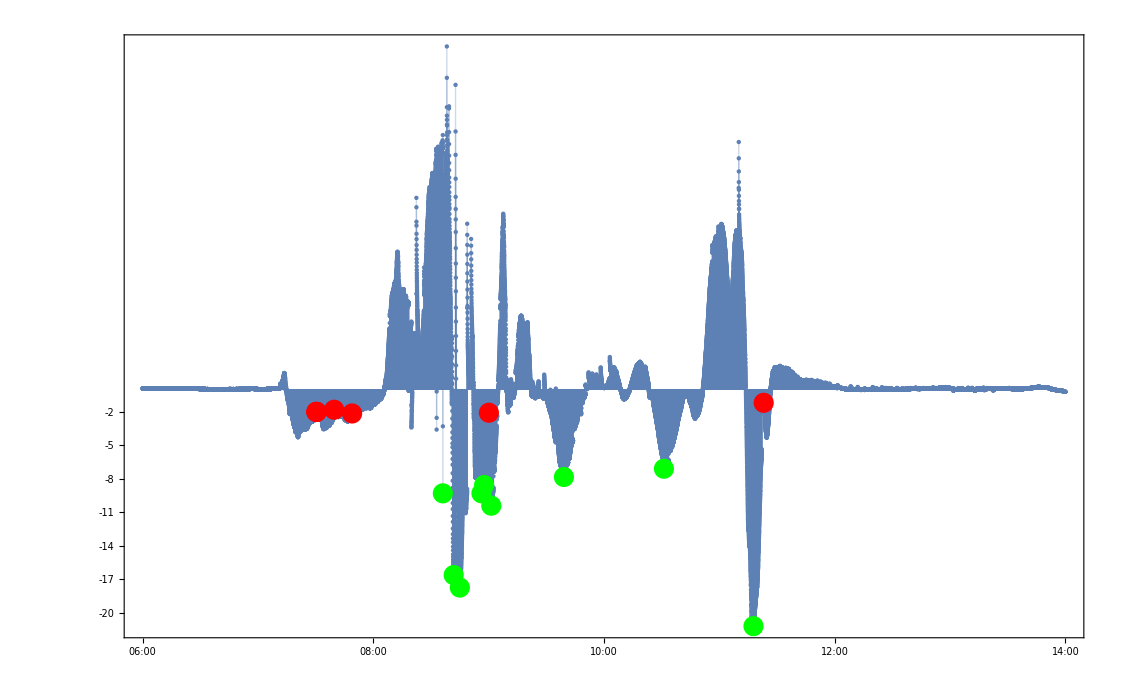

```mathematica
Show[
	plotEField,
	DateListPlot[
		eFieldMaxs,
		PlotStyle->Red,
		PlotRange->eFieldPlottingRange,
		Joined->False
	],
	DateListPlot[
		eFieldMins,
		PlotStyle->Green,
		PlotRange->eFieldPlottingRange,
		Joined->False
	]
]
```

## Find the start and end of the peaks

```mathematica
eFieldPeakPositions=Flatten[Position[electricField, #]&/@eFieldMins];
naI3PeakPositions=Flatten[Position[naI3, #]&/@naI3Maxs];
```

```mathematica
naI3PeakPositions
```

{862,960,1364,1955,1958,2120,2382,3467,3644}

```mathematica
(*P art[electricField,#]&/@eFieldPeakPositions; *)
```

```mathematica
naI3PeakPositions[[Length[naI3PeakPositions]]]
```

3647

```mathematica
naI3[[Length[naI3]]][[2]]
```

49764

```mathematica
Which
```

```mathematica
(* Example of Function usage: moveToRight[electricField, eFieldPeakPosition, 2, 1200] *)
moveToRight[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer, triggerThreshold_] := (Module[
{wndSize, wndStep},
Which[
	(peakPositions[[1]] - windowSize) < 1,
		(wndSize = peakPositions[[1]] - First[data][[2]];
		wndStep = wndSize),
	((Last[data][[2]] - 1) - Last[peakPositions][[2]] < windowSize),
		(wndSize =  Last[data][[2]] - Last[peakPositions];
		wndStep = wndSize),
	True,
		(wndSize = windowSize;
		wndStep = wndSize)
];
Select[
	Transpose[{
		Range[1, wndSize+1, windowStep],
		TimeSeriesAggregate[
			Part[
				data[[All,2]],
				Span[Part[peakPositions,peakN], Part[peakPositions,peakN]+wndSize]
			],
			windowStep
		]
	}],
	(#[[2]] ≤ triggerThreshold)&
]]);

moveToRight[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer] := (Module[
{wndSize, wndStep},
Which[
	(peakPositions[[1]] - windowSize) < 1,
		(wndSize = peakPositions[[1]] - First[data][[2]];
		wndStep = wndSize),
	((Last[data][[2]] - 1) - Last[peakPositions][[2]] < windowSize),
		(wndSize =  Last[data][[2]] - Last[peakPositions];
		wndStep = wndSize),
	True,
		(wndSize = windowSize;
		wndStep = wndSize)
];
Transpose[{
	Range[1, windowSize+1, windowStep],
	TimeSeriesAggregate[
		Part[
			data[[All,2]],
			Span[Part[peakPositions,peakN], Part[peakPositions,peakN]+windowSize]
		],
		windowStep
	]
}]]);
```

```mathematica
(* Example of Function usage: moveToLeft[electricField, eFieldPeakPosition, 2, 1200] *)
moveToLeft[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer, triggerThreshold_] := Module[
{wndSize, wndStep},
Which[
	(peakPositions[[1]] - windowSize) < 1,
		(wndSize = peakPositions[[1]] - First[data][[2]];
		wndStep = wndSize),
	((Last[data][[2]] - 1) - Last[peakPositions][[2]] < windowSize),
		(wndSize =  Last[data][[2]] - Last[peakPositions];
		wndStep = wndSize),
	True,
		(wndSize = windowSize;
		wndStep = wndSize)
];
Select[
	Transpose[{
		Range[-windowSize-1, -1, windowStep],
		TimeSeriesAggregate[
			Part[
				data[[All,2]],
				Span[Part[peakPositions, peakN]-windowSize, Part[peakPositions, peakN]]
			],
			windowStep
		]
	}],
	(#[[2]] ≤ triggerThreshold)&
]];

moveToLeft[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer] := Module[
{wndSize, wndStep},
Which[
	(peakPositions[[1]] - windowSize) < 1,
		(wndSize = peakPositions[[1]] - First[data][[2]];
		wndStep = wndSize),
	((Last[data][[2]] - 1) - Last[peakPositions][[2]] < windowSize),
		(wndSize =  Last[data][[2]] - Last[peakPositions];
		wndStep = wndSize),
	True,
		(wndSize = windowSize;
		wndStep = wndSize)
];
Transpose[{
	Range[-windowSize-1, -1, windowStep],
	TimeSeriesAggregate[
		Part[
			data[[All,2]],
			Span[Part[peakPositions, peakN]-windowSize, Part[peakPositions, peakN]]
		],
		windowStep
	]
}]];
```

```mathematica
rightEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer, triggerThreshold_] := Part[
	data,
	(Part[
		Select[
			moveToRight[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToRight[data, peakPositions, peakN, windowSize, windowStep, triggerThreshold][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];

rightEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_Integer] := Part[
	data,
	(Part[
		Select[
			moveToRight[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToRight[data, peakPositions, peakN, windowSize, windowStep][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];
```

```mathematica
leftEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_, triggerThreshold_] := Part[
	data,
	(Part[
		Select[
			moveToLeft[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToLeft[data, peakPositions, peakN, windowSize, windowStep, triggerThreshold][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];

leftEdge[data_, peakPositions_, peakN_Integer, windowSize_Integer, windowStep_] := Part[
	data,
	(Part[
		Select[
			moveToLeft[data, peakPositions, peakN, windowSize, windowStep],
			#[[2]]==Min[moveToLeft[data, peakPositions, peakN, windowSize, windowStep][[All,2]]]&
		],
		1,
		1
	] + peakPositions[[peakN]])
];
```

```mathematica
eFieldRightEdges=(rightEdge[electricField,eFieldPeakPositions,#,1200, 30, 0])&/@Range[1,Length[eFieldPeakPositions]];
eFieldLeftEdges=(leftEdge[electricField,eFieldPeakPositions,#,1200, 30, 0])&/@Range[1,Length[eFieldPeakPositions]];
```

```mathematica
naI3RightEdges=(rightEdge[naI3,naI3PeakPositions,#,20, 1])&/@Range[1,Length[naI3PeakPositions]];
naI3LeftEdges=(leftEdge[naI3,naI3PeakPositions,#,20, 1])&/@Range[1,Length[naI3PeakPositions]];
```

Part::take: Cannot take positions -18 through 2 in {50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,«4142»}.

Transpose::nmtx: The first two levels of {{-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1},TimeSeriesAggregate[{50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,«4142»}⟦-18;;2⟧,1]} cannot be transposed.

Part::take: Cannot take positions -18 through 2 in {50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,«4142»}.

Transpose::nmtx: The first two levels of {{-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1},TimeSeriesAggregate[{50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,«4142»}⟦-18;;2⟧,1]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Part::partw: Part 1 of Transpose[] does not exist.

Part::pkspec1: The expression 2+Transpose[]⟦1,1⟧ cannot be used as a part specification.

```mathematica
moveToLeft[naI3,naI3PeakPositions,1,20, 1]
```

Part::take: Cannot take positions -18 through 2 in {50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,«4142»}.

Transpose::nmtx: The first two levels of {{-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1},TimeSeriesAggregate[{50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,«4142»}⟦-18;;2⟧,1]} cannot be transposed.

Transpose[{{-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1},TimeSeriesAggregate[{50292,51027,50914,50789,50618,50652,50591,50621,50720,50741,49945,50206,50216,50592,50598,50197,50255,50370,50046,50030,50027,49910,50472,50180,50198,50377,50125,49923,49810,50397,49993,50360,50288,49643,50210,50064,50068,49476,50471,50077,50013,50162,49843,49996,50301,50117,49903,49948,50254,49406,49498,49969,49592,49610,50055,49538,49963,49660,50145,49627,49865,49687,50001,49914,49703,49714,49973,49461,49499,49531,49777,49567,49668,49931,49149,49427,49308,49442,49221,49376,49228,49109,49536,49391,49459,49692,49275,49409,49376,49627,49296,49608,49410,49361,49560,49135,49215,49151,49686,49470,49300,48945,49328,49095,48872,49205,49287,49316,49148,49302,49049,49292,49596,49522,49433,49314,49211,49184,49224,49149,49373,49001,49728,49353,49341,48996,49375,49170,48896,49141,49094,48959,49108,49209,49222,49177,49307,49268,48986,49179,49306,49102,49392,49161,48913,49370,49445,49564,49521,49267,49073,49147,48914,49178,49011,49113,49227,49041,48941,49380,49389,49192,49240,49288,49386,48889,49541,48919,48935,49637,49007,49142,48989,48910,49016,48953,49030,49011,49105,49390,49426,49127,49498,49094,49311,49421,49108,49314,48871,49438,49339,49055,49184,49066,49148,49072,49128,49323,49423,48563,49001,48838,49106,49274,49238,49114,49056,48862,49213,49277,49087,49680,49171,49283,48989,49499,49230,49095,49217,49382,49362,49137,49131,49520,49256,49355,49075,49800,49592,49162,49322,49538,49882,49539,49666,49579,49193,49482,49293,49280,49754,49593,49193,49204,49709,48981,49226,49612,49636,49349,49381,49440,49363,49170,49288,49489,49410,49626,49609,49570,50025,49697,49317,49278,49365,49549,49695,49772,49649,49685,49832,49687,49880,49746,49892,49624,49700,49727,49675,49574,49751,49929,49629,49363,49825,49338,49411,49640,50030,49439,49921,49598,50142,49752,49947,49639,49672,49542,49704,49357,49621,49648,49791,49711,50019,49825,49326,50045,50199,49772,49773,49931,49804,49646,50006,49914,50415,49892,50055,49943,50413,49982,50336,50438,50388,50420,49740,50381,50241,50008,50360,50582,50128,50424,50507,50649,50191,50789,50569,50727,50391,50229,50628,50492,50248,50724,50351,50641,50662,50645,50961,50545,50450,50503,50436,51352,50681,50546,50487,50780,50789,50632,50817,51233,50706,50756,51078,51097,50797,50613,50719,50738,50825,50817,50976,51205,50789,51234,51541,51157,51113,51175,51127,51053,50761,51369,51204,51329,50844,51433,51400,51052,51152,51082,51139,50881,51489,50944,51342,51428,51288,51308,51678,51126,51562,51695,51749,51468,51540,51640,51687,51961,51444,50987,51449,51454,51693,51478,51729,51963,52127,51985,51950,51578,51629,51954,52160,51969,52067,52111,51349,52080,51999,51859,52057,52239,52449,52319,52050,52091,51908,52481,52410,52293,52452,52312,52522,52424,52230,52690,52576,52628,52269,52713,52671,53028,52616,52987,52705,52449,52616,52517,52741,53027,52638,53163,53364,53198,52975,53133,53166,52977,53103,53216,52554,52832,52472,53133,52544,53302,52666,53096,53111,53273,52917,53242,52966,53264,53197,52937,53501,53507,53252,53192,53102,53754,53275,53267,53252,53560,53484,53402,53593,53564,53476,52846,53549,53933,53744,53816,53245,53621,53522,53711,53831,53630,53711,53873,53988,53626,53906,53797,53820,54012,53542,53917,54068,53731,53696,53708,53568,54417,53928,54031,53666,53789,53742,53953,54531,53919,53775,53744,54267,54397,53951,53679,54231,54124,54176,54101,54314,54368,53738,54518,54242,53839,54178,54464,54615,54056,53894,54476,54447,54489,54476,54796,54321,54212,54884,54373,54253,54409,54444,54354,54240,54303,54953,54175,54617,54718,54560,54439,55154,54154,54421,54452,54242,54615,54887,54252,55039,54862,54478,54338,55025,54681,54395,54536,54881,54616,54287,54480,54835,54463,54596,55034,54800,54523,55180,54602,55248,55421,55003,55285,55048,55282,55275,55050,54928,55332,55108,54809,55280,54899,54976,55012,55113,55350,55364,55188,55316,54772,54928,54931,55009,55310,55277,55194,55131,55687,55268,55098,55240,55278,55267,55493,55752,54983,55257,55204,55553,55321,54880,55340,55277,55739,54966,55034,55715,55680,55234,55265,55240,55296,55283,54955,55178,55395,55552,55334,55566,54995,55536,55533,55307,55325,55575,55366,55352,55161,55474,55980,54970,55147,55479,55459,55165,55454,55146,55234,55280,55475,55513,55333,55841,55543,55235,55525,55736,55561,55426,55226,55215,55449,55227,55324,55136,55680,55303,55755,55274,55977,55823,55192,55427,55262,55575,55590,55681,55600,55094,55540,55418,55339,55146,55481,55459,55029,55184,55307,54932,55232,55391,55256,55011,55322,55600,54883,55152,55202,55379,55156,55294,55167,54856,55616,55221,55083,55261,55234,55223,55024,54921,55385,55174,55000,55055,55662,55215,55058,55069,55525,55192,54995,55118,54790,54800,55032,55050,54717,54449,55332,55255,54944,55164,55036,54882,55067,54932,54989,54880,54701,55517,54995,54950,54443,54908,55068,54723,54875,54876,55082,54335,54534,54761,54582,54902,55241,55022,54612,55080,54848,54833,54974,54875,54717,54522,54865,54684,54529,55231,54882,54950,54890,55004,55037,55201,55130,54724,55161,55599,54779,54832,55196,54873,54930,55491,55355,55640,56081,56723,57871,58922,59788,61773,61980,62335,61912,62051,61839,62247,62774,63134,63310,63456,63162,63596,63403,63154,63598,63883,63353,64255,63911,63920,64660,65158,65227,65458,66146,66345,66560,66358,66390,66978,66709,66841,65881,65928,66100,66072,65300,65155,65047,65010,65104,65135,65279,65423,65165,64742,64673,64858,65050,64591,64612,64338,64205,63515,63840,63583,63777,63675,64149,63667,63836,63214,62962,63273,63671,62970,62961,62704,62894,63172,62438,62255,62202,62145,61960,61627,62176,61337,61334,61657,61134,61387,61211,61438,61085,60946,60636,60525,60550,60944,60492,60771,60404,60897,60179,60826,60585,60438,60182,60282,59978,59922,60433,59798,59986,60441,59722,60466,60691,60131,60146,60240,59700,59885,59995,59746,60194,60002,60338,60598,60457,60274,59937,60231,60851,60831,60869,61359,61299,60809,60279,60747,60997,61028,60551,60296,60755,60561,60660,60502,60767,60161,60691,60685,60308,60266,60644,60854,60660,60504,59985,60483,60318,60907,60426,60118,60431,60363,60770,60317,60173,60141,59777,59776,59652,59631,58878,59312,58876,58712,58488,58244,58618,58152,58157,58022,57983,58416,57964,58091,57401,57897,57820,56950,57349,56761,56741,56849,56920,56587,56279,56630,56270,56513,56574,56001,55646,55927,56053,55857,55324,56003,55560,55481,55417,55404,55447,54911,55142,54954,54710,54984,54745,54977,55026,54465,54320,53839,54277,53932,54212,54364,54006,54012,54126,53757,53638,53655,53606,53903,53546,53559,53543,53780,53718,53502,53370,53523,52771,52727,53040,52806,52825,52911,52569,52479,52745,52537,52711,52870,52597,53016,52560,52392,52452,52107,52295,52302,52299,51821,52266,52256,52616,52024,52275,52355,52238,51842,52442,52147,52109,52082,51973,51621,51655,51921,51801,52142,52412,51689,51529,51292,51847,51742,52113,51419,51524,51744,51075,51516,51527,51354,51372,51514,51474,51781,51479,51411,51752,51371,51088,51671,51159,51615,51279,51241,51356,51616,51567,51090,51462,51358,50897,51409,50874,51295,51201,51199,51187,50832,51149,51412,50896,50939,51157,51102,51298,51136,51177,51086,50784,51136,50912,50778,51120,50891,50877,50982,51123,50791,50689,50670,50813,50981,50861,50961,50931,50714,50768,51271,51038,51462,50707,50846,50515,50543,51021,50846,50951,50755,50925,50771,51029,51046,50642,50947,50719,50865,51146,50590,50648,50913,50720,50556,50821,50767,50107,50703,50335,51049,50392,50646,50817,50882,50494,50346,49979,50252,50454,51040,50020,51056,50237,50595,50605,50500,50463,50081,50393,50448,50493,50765,50550,50623,50283,50342,50536,50593,50225,50445,50318,50738,50374,50470,50406,51095,50477,50275,50448,50702,50507,50263,50477,50542,50125,50460,50214,50364,50465,49963,49876,50567,49868,50368,50308,50425,50369,50288,50246,50818,50429,50234,50196,50549,50383,50462,50366,50236,50297,50067,50341,50198,50494,50573,50196,50298,50222,50013,49975,50500,50378,50004,50116,50196,50871,50003,50531,50390,50223,50352,50166,50301,49874,50364,49880,50507,49899,50325,49896,50123,50257,50223,50367,49889,50145,50281,50095,50039,50646,50413,50027,50526,50120,50204,50396,50455,50405,50037,50475,50532,50223,50536,50041,50302,50634,50721,50314,50253,50107,50332,50588,50387,51070,50963,51070,51770,51297,51357,51530,51422,51370,51350,50802,50893,51238,51072,51667,51108,51360,51519,51459,51966,51704,50965,51202,51169,51113,51394,51255,51478,51742,51228,51362,51426,51169,50980,51261,51539,51621,50990,51101,51194,50978,51429,50849,51046,51041,50780,51249,50805,50878,51004,50814,50726,50692,50724,50687,50574,50762,50461,50515,50460,50582,50397,50436,50367,50631,50484,50460,50884,50589,50755,50611,50803,50266,50674,50262,50415,50312,50604,50445,50385,50467,50324,49892,50433,50170,50423,49812,49684,50341,50103,50155,50252,50399,49902,49868,50223,49849,50007,50260,49937,49920,50286,50358,50200,50365,50175,49985,50065,49976,49870,49884,49957,49833,50007,49930,49966,50105,49656,50006,50203,50131,49887,49798,49593,49915,49765,49613,49405,49860,49668,49642,49690,49798,49528,49743,49749,49842,49675,49770,49788,49642,49676,49512,49435,49695,49690,49452,49717,49791,49927,49421,50041,49562,49737,49913,49321,49519,49859,49362,49661,49705,49309,49939,49462,49526,49784,49329,49344,49427,49392,49389,49474,49670,49140,49469,49440,49691,49225,49511,49695,49712,49652,49693,49314,49502,49219,49466,49702,49064,49319,49387,49234,49580,49345,49552,49144,49382,49239,49648,49679,49417,49263,49731,49386,49203,49601,49509,48876,49608,49351,49492,48958,49504,49218,49450,49262,49510,49675,49508,49420,49259,49521,49373,49496,49017,49389,49491,48840,49167,49120,49417,49300,49531,49403,49375,49488,49146,48876,49225,49279,49406,49711,48951,49323,49162,48902,49635,49103,49310,49215,48875,49115,49286,49880,49044,48743,49356,49226,49295,49279,48897,49310,49766,49479,49563,49242,49252,49454,48876,49530,49578,49071,48917,49380,49010,49203,48653,49116,49384,49004,49023,49211,49234,49054,49356,49352,48770,49191,48965,49104,49316,49306,49424,49365,48981,49056,49412,49504,49039,48840,49491,49157,49029,49327,49209,48930,49197,49059,48972,48784,48954,49236,49123,49211,48878,49235,49591,49167,49215,49120,49402,49518,49726,49339,49475,49760,49587,49498,49293,48981,49688,49452,49654,49639,49840,49390,49747,49692,49910,49680,49493,49603,49989,49758,49964,49575,49724,49549,49232,49507,49696,49598,49635,49855,49900,49695,49661,49250,49602,50039,49537,49738,49777,49882,49769,49583,49927,49801,49639,49754,49382,50051,49569,49683,49647,49294,50111,49564,49701,49718,50022,49951,49538,49889,49513,49730,49675,49509,49814,50012,49649,49967,49965,49978,49769,49322,50017,49850,50244,50298,49667,49821,49876,50086,49975,49895,49747,49965,49768,49915,50110,49949,49796,50110,50018,50006,49748,49936,49754,50242,49674,49498,49748,49765,49897,50043,49549,49855,50102,49894,50045,49984,50015,50023,49566,49848,49925,49797,50150,50021,50247,50090,50193,50372,49744,49747,49943,50144,50073,50232,50197,50020,49963,50106,50087,50127,49981,49930,50265,49876,50595,49565,50159,50049,50327,50015,50373,50449,50254,49910,50051,50080,50430,49790,50039,50830,50274,50162,50207,49714,50515,50133,50380,50627,50578,49989,50345,50479,50273,50100,50482,50413,50110,50245,50061,50177,50345,50250,50199,49928,49800,50505,50872,50485,50274,49999,50405,49697,50272,50448,50473,50422,50384,50951,50598,50389,50347,50415,50267,50420,50486,50737,50803,51079,50823,50881,51291,52061,52587,52864,52824,52686,52821,53150,52889,53099,52682,53080,53276,53336,53210,53447,53755,53721,53883,53817,53399,53644,53458,53468,53379,54221,52983,53215,53644,53312,53181,52953,53088,53527,53296,53532,53315,53551,53096,53260,53073,52976,53383,53492,52929,53070,53457,52765,52865,53261,52621,52390,52616,52584,52844,52787,52667,53217,53372,53861,53346,53814,53653,53701,54223,54473,54853,55086,55247,55151,55401,55153,55749,55904,56234,55778,56063,56594,59588,56596,57116,57828,57565,57534,58587,57903,58154,58213,57506,57369,57980,57188,56848,57187,57366,57963,57467,57590,57638,56885,57680,57763,57538,57679,57895,57653,58084,57566,57656,57424,57451,57027,57563,56935,57046,57383,57049,56715,57093,56773,56260,56921,56158,56349,56002,56299,56631,56192,56484,56355,55657,55732,56023,55538,55336,55863,55031,55186,55102,54837,54831,54942,54950,54358,54628,54441,55023,54561,54271,53844,54425,54386,53616,53643,53548,53826,53406,53440,53873,52948,53324,53417,53817,53008,52591,52929,52939,52581,52730,52707,52834,53390,53249,52835,53006,53032,52937,52886,52814,53064,52837,53099,52863,52445,52419,51905,52637,52443,52595,52242,52646,52421,52848,52123,52334,52167,52560,52506,52354,52044,51614,51912,52258,52302,52219,52527,52081,52195,52299,51960,52164,52433,51731,51812,51976,51420,52341,51810,52072,51871,52033,51836,52286,51963,52010,52025,51806,51913,52079,51817,51862,52205,52201,52177,52289,52623,52623,52743,52795,52961,52973,53259,53076,53230,53330,53293,53102,53203,53301,53606,53594,53471,53719,53261,53269,52747,53164,52747,52860,52779,52879,52981,53034,52488,52596,52821,52674,52925,52144,52167,51944,52330,52330,52549,52176,52456,52243,52362,52283,51638,52129,52110,52461,52004,51578,51955,52113,51638,51854,51964,52177,52028,51836,51824,51929,51747,51896,51550,51478,51508,51375,51650,51253,51350,51967,51578,51140,51219,51669,51583,51165,50880,51197,51278,51173,50811,51451,51293,51459,51498,51089,51369,50940,51068,50515,51066,51170,51056,50708,51171,50789,50720,50822,51435,51134,50645,51060,51002,50819,50528,51251,51060,51056,51103,50964,50862,50963,50991,50894,50605,51208,51142,50906,51129,50945,50818,50981,50941,50827,50857,50575,50645,50497,50596,50709,51398,51106,50671,51195,50883,50764,50680,50713,50747,50687,50858,50397,51132,50920,50912,50646,50806,50948,50688,50711,50518,50667,50368,50671,50837,50641,50587,50876,50586,50623,50499,51125,50789,50921,50581,50515,50739,50946,50638,50481,51128,50857,50690,50943,51075,50743,50968,51085,50694,51098,50811,51260,51105,51223,51426,51154,51160,51001,51827,50870,51505,51297,51400,50824,51517,51651,51286,51501,51872,51263,51278,51599,51789,51707,51324,51586,51456,51315,51952,51735,51451,52209,51554,51614,51985,52006,51924,51963,51490,52205,52248,51950,52370,52248,52392,52324,52500,52198,52332,52714,52523,52500,52959,52508,52488,52895,52729,52474,53234,52923,52966,52576,53299,52829,53015,52651,52949,52734,53255,53185,53049,53188,53410,53368,53194,53619,53236,53422,53685,53834,53646,53746,53442,53392,53832,53678,54116,54143,54022,54296,54188,54262,53611,54138,54178,53905,54445,54092,54167,54234,53878,53814,54174,54046,54145,53976,54101,54291,53552,53840,53851,53714,53144,53410,53777,53763,53601,53604,53499,53430,53141,52665,53309,53015,53440,53123,53223,52783,53025,52874,52739,52774,52468,52569,52501,52694,52309,52536,52499,52590,52500,52005,51865,51866,51588,52054,51983,51984,52150,52077,51803,52589,51849,51804,52130,51636,52210,51677,51931,52061,51685,51457,51561,51677,51592,51329,51335,51524,51547,51511,51275,51238,51207,51499,51593,51682,51471,51156,51082,51017,51295,50995,51154,50906,51217,50727,50806,51060,51029,50949,50861,50837,50896,50893,50996,50579,50988,50570,50895,50505,51059,50355,50619,50263,50639,50591,50405,50318,50302,50246,50411,50574,50556,50439,50223,49992,49940,49921,50141,49927,50253,49848,49908,49883,50140,50111,50132,49896,49713,49771,49693,49945,49406,49688,49993,49799,49676,49863,49502,50088,49901,49703,49736,49666,49686,49585,49587,49527,49706,49328,49629,49512,49704,50011,49131,49226,49796,49392,49307,49687,49083,49207,49247,49739,49287,49289,49349,49107,49354,49627,49435,49603,49595,49662,49328,49130,49145,49312,49190,49459,49380,49246,48877,49485,49180,49615,48918,49228,49321,48843,49192,49635,49031,49299,48975,49379,48623,49040,49387,49270,48944,49258,48765,49168,48894,48978,49074,49129,49071,49236,49488,49088,48775,48846,49314,48962,49125,49043,48759,49013,48720,49192,48949,49105,49331,48777,48865,48661,49243,49009,49046,49072,48849,48732,48958,49201,48926,49116,48887,49195,48865,48767,49160,48792,49105,48575,48948,49017,48685,49038,48760,48830,49037,49317,49055,48973,48387,48807,49107,48577,48604,48781,48576,48931,48751,48785,48530,48446,48728,48804,48564,48980,48564,48828,48421,48937,48871,48862,48628,48975,49035,48799,48199,48943,48706,48977,49094,48824,48978,48470,48655,48961,48985,48805,48564,48959,48300,48709,48403,48706,48422,48636,48787,48247,48647,48692,48511,49085,49223,48764,48485,48504,48457,48721,48909,48903,48015,48972,48642,48360,48546,48372,48725,48749,48555,48424,48438,48731,48822,48764,48774,48737,48561,49207,48807,48837,48740,48865,48890,48700,48649,48560,48807,48724,48474,48218,48626,48322,48700,48898,48670,48506,48730,48412,48798,48567,48171,48632,48599,49023,48675,48743,48453,48179,48853,48619,48558,48556,48163,48638,48504,48334,48060,48562,48878,48784,48338,48101,48758,48544,48534,48514,48759,48758,48638,48649,48327,48444,48289,48894,48825,48232,48208,48788,48634,48399,48926,48562,48533,49012,48421,48586,48693,48538,48302,48428,48661,48421,48607,48744,48717,48874,48471,48340,48423,48594,48432,48566,48412,48426,48759,48422,48716,48608,48351,48334,48296,48595,48522,48599,48283,48282,48076,48410,48126,48515,48271,48552,48219,48477,48280,48214,48198,48445,48730,48941,48375,48661,48224,48450,48466,48589,48443,48229,48525,48346,48316,48341,48713,48341,48517,48238,48540,48623,48586,48681,48479,48116,48379,48432,48293,48259,48235,48363,48331,48268,48114,48449,48590,48421,48384,48596,48397,48061,48740,48433,48804,48330,48483,48469,48513,48622,48461,48462,48863,48855,48676,47844,48380,48619,48535,48525,48186,47810,48196,48226,48488,47881,48420,48450,48243,48356,48487,48463,48459,48709,48407,48344,48278,48692,48475,48744,48177,48404,48385,48298,48532,48855,48852,48572,48351,48643,48508,48296,48415,47996,47953,48672,48403,48321,48754,48098,48137,48138,48590,48556,48602,48189,48830,48412,48296,48655,48129,48168,48408,48499,48359,48419,48391,48609,48594,48285,48555,48041,48899,48099,48597,48252,48409,48516,48800,48289,48430,48079,48066,48499,48591,48320,48083,48471,48793,48499,48225,48223,48538,48659,48420,48572,48252,48333,48745,48327,48246,48382,48171,48243,47778,48010,48419,48378,48390,48641,48711,48548,48365,48177,47978,48394,47942,48377,48807,48517,48330,48148,48490,48128,48196,48321,48356,48606,48236,48512,48355,48185,48344,48417,48615,48301,48021,48204,48570,48411,48287,48789,48233,48139,48484,48625,47976,48474,48712,48431,48199,48637,48198,48152,48315,48750,48602,47970,48553,48450,48246,48053,48203,48732,48258,48076,48190,48635,48542,48395,48235,48268,48438,48483,48678,48211,48242,48874,48158,48446,48373,48589,48811,48713,48536,48059,48384,48046,48436,48614,48605,48459,48754,48606,48378,48567,48399,48552,48429,48476,48355,48456,48278,48551,48595,48463,48532,48411,48133,48220,48278,48392,48368,48776,48549,48417,48895,48657,48171,48472,48519,48668,47850,48907,48466,48986,48444,48333,48619,48393,48385,48671,48351,48692,48578,48661,48624,48611,48719,48095,48492,49033,48779,49025,48622,49043,49346,48800,48553,48727,48741,48701,48469,48695,48659,48455,48920,48951,49064,48954,48983,48484,48716,48552,48408,48788,49263,48769,49149,49376,48731,48978,48856,48982,48884,49075,48937,48984,49162,48458,49047,48865,48858,48886,49137,48871,49137,48877,49134,49096,49231,49239,49260,48822,49390,49371,49412,49205,49171,49042,49457,49586,49171,49380,48871,49213,49399,49597,49285,49613,49307,49359,49607,49581,49149,48957,49911,49794,49774,49755,49541,49506,48987,49793,49093,49426,49898,49536,50055,49925,49893,50017,49548,49572,49807,49880,50176,49547,49892,49878,49931,49773,49691,50175,50108,50350,49893,50207,49956,50313,50235,50638,50378,50051,50011,50017,50277,50737,49589,50410,50062,50315,50460,50201,50478,50577,50598,50045,50002,50486,50166,50634,50318,50192,50464,50216,50424,50862,50607,50348,50703,50503,50356,50395,50908,50843,50779,50719,50811,50963,50528,50945,51023,50860,50998,51019,51039,51128,51319,51161,50842,51244,51083,50876,50988,51390,51282,51052,51278,50800,51034,51017,51507,51275,51463,51726,51632,51543,51323,51198,51316,51415,51156,51281,51474,51235,51723,51487,51520,51604,51281,51384,51871,51983,51660,51611,52115,51561,51573,51809,51595,51521,51879,51709,52196,51858,51789,51877,51910,51635,52196,52113,51978,51614,52520,52151,52212,52099,51868,51854,51925,52100,51909,51654,51873,51878,51945,52153,52366,51975,51778,52190,52013,52235,52011,52269,51918,52419,52493,52175,52277,52161,52299,51966,52262,52210,52259,52031,51983,52241,52274,52389,52523,52462,52401,52328,52446,52344,52644,52461,52403,52496,52601,52455,52731,52405,52094,52646,52475,52617,52270,52669,52270,52821,52740,52505,52597,52627,52834,52156,52284,52355,52698,52682,52538,52527,52551,52507,52157,52323,52940,52804,52956,52573,52585,52599,52939,53125,52965,53842,53334,53618,54019,53023,53733,53218,53499,53853,53362,53982,53963,54123,54150,54185,54717,54497,54563,54264,54285,54424,54146,54257,54388,54720,54409,54561,54485,54869,54493,54856,55030,55010,54828,55155,55612,55068,55549,55725,55553,55287,55872,55821,55859,55837,55572,55480,55848,55618,55736,56292,55701,55584,55584,55746,55359,55474,55369,55016,55210,55338,55019,55354,54947,54724,54754,54912,55027,54883,54961,54657,55323,54426,54420,54666,54402,54446,54577,54545,54491,54148,54002,54286,54222,54310,54694,53763,54549,54055,54234,53767,54194,53718,53872,53667,53668,53790,53764,53663,53392,54042,53927,53773,53983,53600,54067,53524,53546,53897,53372,53408,53320,53470,53613,53834,53043,53510,53695,53470,53656,53452,53432,53174,53242,53520,53065,53430,53646,53408,53343,53225,53157,53560,53232,53334,53503,53091,53595,53001,52769,53257,53106,52965,52990,53079,52867,52909,53398,53659,53610,53193,52636,53121,52868,52895,52741,53134,53137,52695,53559,53252,52992,53065,53194,53364,53527,53098,53022,52952,53336,53045,52981,53238,52794,52896,52903,53117,52872,53231,53483,53043,53021,52968,53378,52883,53146,52843,53076,52734,52936,53291,52613,53489,52594,53461,52803,53124,52360,52814,52937,52837,53466,53129,53179,53214,53048,52488,52993,53062,53093,52873,52582,53099,53060,52922,52617,53002,53223,53234,53652,53685,54051,53732,53658,53527,53783,53689,54200,54152,54112,53909,53921,53966,54429,53576,54092,53634,54248,54206,53834,54013,53661,53739,53591,53882,54229,53324,53813,53708,53924,53685,53902,53679,53916,53741,53667,53428,53684,53330,53427,53628,53567,53190,53049,53771,53409,53457,53731,52852,53120,53319,52801,53311,53353,53406,53430,53308,53312,53571,53386,52915,53325,53390,52967,53165,53236,53309,53201,52639,53357,53319,52904,53241,53539,53208,53108,53225,52831,52929,53013,52441,53099,52982,52923,52842,53314,52793,52477,52897,52568,52395,52922,52592,53013,52807,52801,52984,52984,52474,52412,52740,52554,52313,52419,52424,52712,52721,52514,52415,52299,52573,52646,53216,52738,52575,52489,52642,52938,52440,52602,52630,52951,52228,52592,52602,52112,52067,52412,52760,52605,52801,52531,52898,52782,52547,52545,52694,52503,52755,52647,52751,52403,52762,52124,52593,52427,51923,52306,52458,52424,52434,52635,52667,52699,52305,52423,52447,52470,52060,52456,52643,52709,52325,52349,51861,52096,52309,52604,52541,52590,52510,52479,52411,52564,52050,52090,52387,52519,52416,52496,52399,52463,52620,52536,52210,52364,52452,52325,52323,52077,52293,51667,52365,51741,52227,52149,52310,52487,52382,52388,52354,52142,52041,51780,52222,52641,51949,51905,52530,51706,52037,51703,52101,52238,52085,51934,52173,51956,52233,52008,52082,51892,52181,51753,52563,52279,52071,51826,52263,52028,52097,51974,52329,52568,52230,51809,51787,51982,52044,51793,52191,52253,51823,52172,51827,51961,52010,52364,51829,51889,52517,51924,51936,52176,51545,52075,51930,51852,52043,52161,51701,51839,51852,51875,51630,51946,51818,51498,52338,51786,52068,52049,51871,51708,52171,51832,51759,51807,52298,51387,51708,51750,51933,51865,51917,52062,51911,51997,52270,51379,51914,52050,51962,51686,51895,51833,51946,51856,51681,52000,51887,52155,51776,51521,51767,51816,51614,51544,51417,51570,51689,51347,52015,51691,51453,51712,51471,51704,51343,51319,51878,51924,51784,51765,51175,51504,51449,51533,51504,51503,51799,51322,51443,51391,51876,51182,51693,51790,51492,51531,51437,51701,51199,51139,51476,51705,51242,51390,51386,51419,51380,51869,51649,51707,51551,51609,51515,51252,51589,51293,51166,51093,51237,51587,51463,51597,51328,51358,51267,51434,51244,51221,51697,51511,50885,51561,51200,51416,51399,51415,51552,51414,51730,50937,51430,50957,51251,51654,51699,51180,50837,51789,50948,50788,51339,51139,51117,51063,51096,51009,51392,51547,51338,51260,51337,51354,51586,51243,50765,51159,51333,51061,51361,50898,51110,51188,51294,51250,51478,51377,50941,51080,51327,50371,50858,51384,50311,51034,50976,51087,51017,51018,51029,51156,50963,50388,51090,49963,50862,50738,50617,50713,50638,50930,50969,50851,50982,50910,51034,50972,50932,50978,50865,50620,50443,50926,50637,50769,50599,51038,50305,50113,50413,50146,50452,50671,50792,50867,50976,50443,50654,50296,50929,50892,50915,50150,50829,50628,50889,50607,50790,51017,50521,50142,50603,50238,50366,50748,50758,50403,50575,50382,50689,50294,50510,50171,50577,50587,50216,50468,50519,50457,50557,50333,50703,50206,50797,50306,50875,50538,50584,50544,50389,50649,50519,50376,50450,50341,50388,50486,50507,50340,50372,50089,50718,50337,50676,50409,50613,50587,50525,50513,50474,50633,50201,50457,50558,50306,50590,50343,50103,50571,50450,50603,50174,50358,50456,50431,50369,50115,50639,50399,49764}⟦-18;;2⟧,1]}]

```mathematica
eFieldLeftEdges
eFieldRightEdges
```

{{{2016,7,6,8,36,9.},22.8225},{{2016,7,6,8,41,47.},-16.615},{{2016,7,6,8,44,59.},-17.745},{{2016,7,6,8,44,44.},-17.1375},{{2016,7,6,8,44,37.},-17.7214},{{2016,7,6,8,44,50.},-17.6024},{{2016,7,6,9,39,8.},-7.82143},{{2016,7,6,10,31,9.},-6.95952},{{2016,7,6,11,17,44.},-21.095}}

{{{2016,7,6,8,44,41.},-17.31},{{2016,7,6,8,44,49.},-17.4725},{{2016,7,6,8,45,1.},-17.7095},{{2016,7,6,9,1,16.},-10.1905},{{2016,7,6,9,1,9.},-10.1526},{{2016,7,6,9,1,22.},-10.1474},{{2016,7,6,9,39,40.},-7.2475},{{2016,7,6,10,31,11.},-7.075},{{2016,7,6,11,17,46.},-21.16}}

## Filtering of data with a moving window.

## Detection of correlation between different time series.

## Detection of TGE events based on existing criteria.

## Detection of hidden correlations of atmospheric data with TGE events.

```mathematica
Partition
Split
```

Smoothing of the derivative of a gaussian